```mathematica
gamma=0.072;
ng=26.43/(8.31*300);
nl=55*10^3;
Deltap=29.35-26.43;
```

```mathematica
DeltaG=4*Pi*r^2*(gamma-1/3*nl*Deltap/ng*r)
```

4 π (0.072-5.04951×10^6 r) r^2

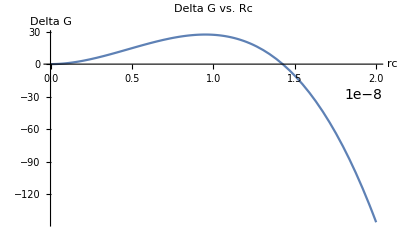

```mathematica
Plot[DeltaG*10^18,{r,0,20*10^-9},PlotLabel->"Delta G vs. Rc",AxesLabel->{rc,Delta G}]
```

```mathematica
Solve[(P+a*n^2/V^2)*(V-b*n)-1/c*(U+a*n/V)==n*R*T-1/c*(U+a*n/V),T]
```

{{T→((-b n+V) (a n^2+P V^2))/(n R V^2)}}

```mathematica
T=(-b*n+V)(a*n^2+P*V^2)/(n*R*V^2)
```

((-b n+V) (a n^2+P V^2))/(n R V^2)

```mathematica
Expand[T]
```

-(b P)/R-(a b n^2)/(R V^2)+(a n)/(R V)+(P V)/(n R)

```mathematica
DT=D[Expand[T],V]
```

P/(n R)+(2 a b n^2)/(R V^3)-(a n)/(R V^2)

```mathematica
oneoveralpha=Expand[V*DT]
```

(2 a b n^2)/(R V^2)-(a n)/(R V)+(P V)/(n R)

```mathematica
v=n/V;
```

```mathematica
e1=b/v;
e2=a/(R*T*v);
```

```mathematica
Expand[Simplify[Factor[T*(1+e1-2*e2)]]]
```

T-(2 a V)/(n R)+(b T V)/n

```mathematica
FullSimplify[(2 a b n^2)/(R V^2)-(a n)/(R V)+(P V)/(n R)-T+(2 a V)/(n R)-(b T V)/n]
```

(a (2 b n^3-n^2 V+2 V^3)+V^2 (P V-R T (n+b V)))/(n R V^2)